# B27

## Error Functions

Units in VOLTS

```mathematica
errorVolt[reading_,range_]:=0.025*reading+If[range=="1V",0.008*1,If[range=="10V",0.006*10,If[range=="100V",0.005*100]]]
```

Units in mA

```mathematica
errorCurrent[reading_,range_]:= 0.05*reading+If[range=="10mA",0.015*10]
```

## 2.1

```mathematica
xdata21={-13.482,-12.212,-10.4940,-9.0400,-7.5012,-6.0031,-4.5000,-2.9997,-1.5080,0.19500,0.39823,0.60783,0.80623,1.00591,1.2160,1.2560,1.1006,0.7066,0.9055,-15.017}
ydata21={-0.0179,-0.0157,-0.0127,-0.0104,-0.0082,-0.0061,-0.0044,-0.0030,-0.0020,0.1739,1.2045,2.9011,4.8051,7.0098,9.4780,9.9692,8.1145,3.8000,5.8540,-0.0208}
measurementRange21=Join@@{ConstantArray[{"100V","10mA"},2],ConstantArray[{"10V","10mA"},7],ConstantArray[{"1V","10mA"},5],ConstantArray[{"10V","10mA"},3],ConstantArray[{"1V","10mA"},2],{{"100V","10mA"}}};
measurementRangeX21=measurementRange21[[All,1]]
```

{-13.482,-12.212,-10.494,-9.04,-7.5012,-6.0031,-4.5,-2.9997,-1.508,0.195,0.39823,0.60783,0.80623,1.00591,1.216,1.256,1.1006,0.7066,0.9055,-15.017}

{-0.0179,-0.0157,-0.0127,-0.0104,-0.0082,-0.0061,-0.0044,-0.003,-0.002,0.1739,1.2045,2.9011,4.8051,7.0098,9.478,9.9692,8.1145,3.8,5.854,-0.0208}

{100V,100V,10V,10V,10V,10V,10V,10V,10V,1V,1V,1V,1V,1V,10V,10V,10V,1V,1V,100V}

```mathematica
Length/@{xdata21,ydata21,measurementRange}
```

{20,20,20}

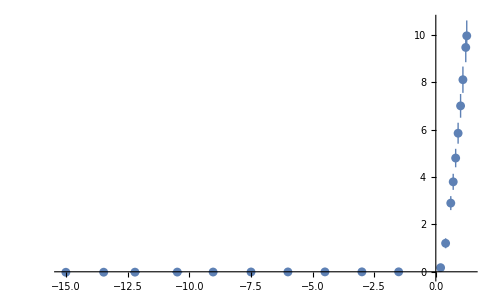

```mathematica
ListPlot[Transpose[{Table[Around[xdata21[[i]],errorVolt[xdata21[[i]],measurementRangeX21[[i]]]],{i,1,Length[xdata21]}],Around[#,errorCurrent[#,"10mA"]]&/@ydata21}]]
```

## 2.2

```mathematica
xdata22={0.08775,0.10780,0.19150,0.40583,0.46618,0.58712,0.61722,0.64693,0.70046,0.71923,0.76200,0.78893};
ydata22={0,0.0001,0.0001,0.0145,0.0713,1.0351,1.6921,2.6183,4.9500,5.9551,8.0510,10.2594};
```

```mathematica
Length/@{xdata22,ydata22}
```

{12,12}

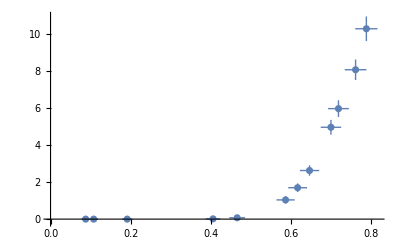

```mathematica
ListPlot[Transpose[{Around[#,errorVolt[#,"1V"]]&/@xdata22,Around[#,errorCurrent[#,"10mA"]]&/@ydata22}]]
```

## 2.3

```mathematica
xdata23=-{1.0874,2.0561,3.0324,4.0110,5.0578,6.0195,7.0213,8.0220,9.0431,11.901,12.016,11.953,12.124};
ydata23=-Join@@{ConstantArray[0,9],{0.7765,5.7150,2.8108,10.6471}};
measurementRange23=Join@@{ConstantArray["10V",10],ConstantArray["100V",3]};
```

```mathematica
Length/@{xdata23,ydata23,measurementRange23}
```

{13,13,13}

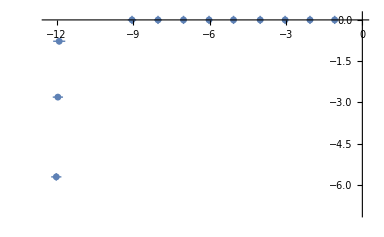

```mathematica
ListPlot[Transpose[{Table[Around[xdata23[[i]],errorVolt[xdata23[[i]],measurementRange23[[i]]]],{i,1,Length[xdata23]}],Around[#,errorCurrent[#,"10mA"]]&/@ydata23}]]
```

```mathematica
xdata23pt2={0.01182,0.40023,0.68661,0.74500,0.80032,0.82443,0.85063,0.90308};
ydata23pt2={0,0.0001,0.6014,1.8823,4.1736,5.4504,6.9884,10.4746};
```

```mathematica
Length/@{xdata23pt2,ydata23pt2}
```

{8,8}

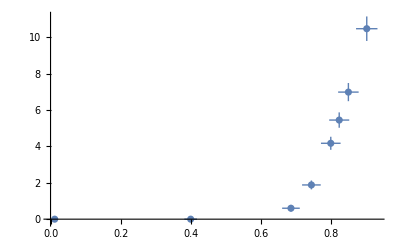

```mathematica
ListPlot[Transpose[{Around[#,errorVolt[#,"1V"]]&/@xdata23pt2,Around[#,errorCurrent[#,"10mA"]]&/@ydata23pt2}]]
```

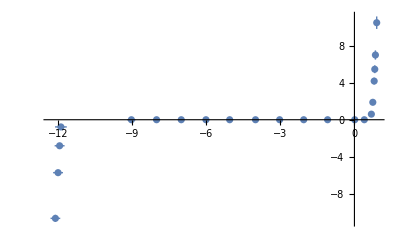

```mathematica
ListPlot[Join[Transpose[{Around[#,errorVolt[#,"1V"]]&/@xdata23pt2,Around[#,errorCurrent[#,"10mA"]]&/@ydata23pt2}],Transpose[{Table[Around[xdata23[[i]],errorVolt[xdata23[[i]],measurementRange23[[i]]]],{i,1,Length[xdata23]}],Around[#,errorCurrent[#,"10mA"]]&/@ydata23}]]]
```

## 2.4

```mathematica
xdata24={3.0137,6.0058,9.0123,12.013,15.030,18.048,21.051,24.015,27.029,30.015}
ydata24={3.0124,6.0033,9.0089,11.889,11.891,11.910,11.926,11.944,11.961,11.977}
measurementRange24=Join@@{ConstantArray["10V",3],ConstantArray["100V",7]}
```

{3.0137,6.0058,9.0123,12.013,15.03,18.048,21.051,24.015,27.029,30.015}

{3.0124,6.0033,9.0089,11.889,11.891,11.91,11.926,11.944,11.961,11.977}

{10V,10V,10V,100V,100V,100V,100V,100V,100V,100V}

```mathematica
Length/@{xdata24,ydata24,measurementRange24}
```

{10,10,10}

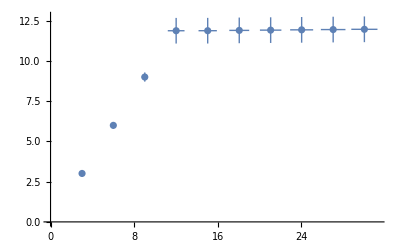

```mathematica
ListPlot[Transpose[{Table[Around[xdata24[[i]],errorVolt[xdata24[[i]],measurementRange24[[i]]]],{i,1,Length[xdata24]}],Table[Around[ydata24[[i]],errorVolt[ydata24[[i]],measurementRange24[[i]]]],{i,1,Length[xdata24]}]}]]
```

## 2.5

```mathematica
xdata25={0.2040,0.4074,0.6037,0.8265,1.0228,1.2000,1.5030,1.5864,1.6512,1.7038,1.7484,1.8073,1.8526,1.9005,1.9545,2.0000};
ydata25=Join@@{ConstantArray[0,7],{0.0054,0.0223,0.0805,0.2035,0.6457,1.4831,3.0669,5.6934,8.4215}}
```

{0,0,0,0,0,0,0,0.0054,0.0223,0.0805,0.2035,0.6457,1.4831,3.0669,5.6934,8.4215}

```mathematica
Length/@{xdata25,ydata25}
```

{16,16}

```mathematica
{errorVolt[#,"1V"]&/@xdata25,errorVolt[#,"10mA"]&/@ydata25}
```

{{0.0131,0.018185,0.0230925,0.0286625,0.03357,0.038,0.045575,0.04766,0.04928,0.050595,0.05171,0.0531825,0.054315,0.0555125,0.0568625,0.058},{0.+Null,0.+Null,0.+Null,0.+Null,0.+Null,0.+Null,0.+Null,0.000135+Null,0.0005575+Null,0.0020125+Null,0.0050875+Null,0.0161425+Null,0.0370775+Null,0.0766725+Null,0.142335+Null,0.210538+Null}}

```mathematica
errorVolt[0,"10mA"]
```

0.+Null

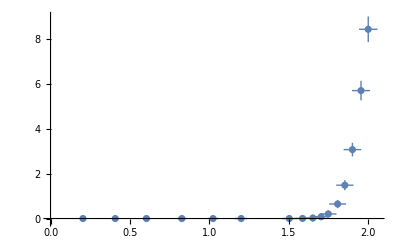

```mathematica
ListPlot[Transpose[{Around[#,errorVolt[#,"1V"]]&/@xdata25,Around[#,errorCurrent[#,"10mA"]]&/@ydata25}]]
```